# Andrea Halenkamp

## Sec 5.2: #2, 4, 5, 8, 10,12

### Problem 2

```mathematica
p2 = {{1,2},{-2,-2}};
TableForm[p2]
```

1 | 2
-2 | -2

```mathematica
{eigenvalues2,eigenvectors2}=Eigensystem[p2]
```

{{1/2 (-1+ⅈ √7),1/2 (-1-ⅈ √7)},{{1/4 (-3-ⅈ √7),1},{1/4 (-3+ⅈ √7),1}}}

### Problem 4

```mathematica
p4 = {{-1,1},{1,-2}};
TableForm[p4]
```

-1 | 1
1 | -2

```mathematica
{eigenvalues4,eigenvectors4}=Eigensystem[p4]
```

{{1/2 (-3-√5),1/2 (-3+√5)},{{1/2 (1-√5),1},{1/2 (1+√5),1}}}

### Problem 5

```mathematica
p5 = {{2,3},{-2,-2}};
TableForm[p5]
```

2 | 3
-2 | -2

```mathematica
{eigenvalues5,eigenvectors5}=Eigensystem[p5]
```

{{ⅈ √2,-ⅈ √2},{{-1-ⅈ/(√2),1},{-1+ⅈ/(√2),1}}}

### Problem 8

```mathematica
p8 = {{2,3},{-1,0}};
TableForm[p8]
```

2 | 3
-1 | 0

```mathematica
{eigenvalues8,eigenvectors8}=Eigensystem[p8]
```

{{1+ⅈ √2,1-ⅈ √2},{{-1-ⅈ √2,1},{-1+ⅈ √2,1}}}

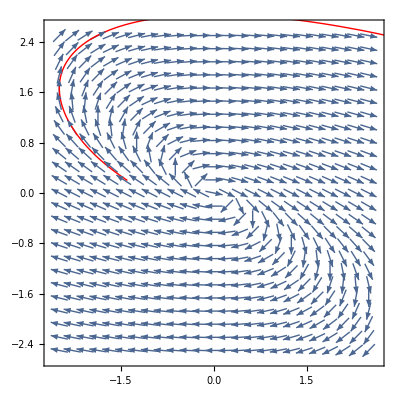

```mathematica
s8=NDSolve[{x'[t]==2x[t]+3y[t],y'[t]==-x[t],x[0]==-1.4,y[0]==0.2},{x,y},{t,10}];
plot8s=ParametricPlot[Evaluate[{x[t], y[t]}/.s8],{t,0,20},PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thick,Red}];
plot8=VectorPlot[{2x+3y,-x},{x,-2.5,2.5},{y,-2.5,2.5},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine];
Show[plot8,plot8s]
```

### Problem 10

```mathematica
p10 = {{-1,1},{1,-2}};
TableForm[p10]
```

-1 | 1
1 | -2

```mathematica
{eigenvalues10,eigenvectors10}=Eigensystem[p10]//N
```

{{-2.61803,-0.381966},{{-0.618034,1.},{1.61803,1.}}}

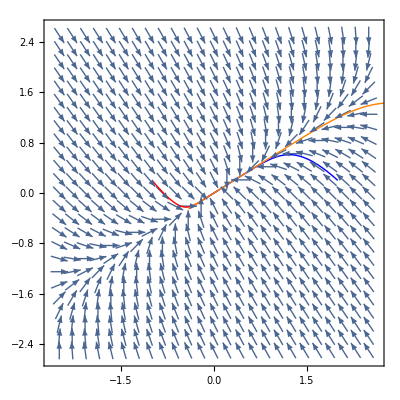

```mathematica
s10a=NDSolve[{x'[t]==-x[t]+y[t],y'[t]==1x[t]-2y[t],x[0]==-1,y[0]==0.2},{x,y},{t,10}];
plot10sa=ParametricPlot[Evaluate[{x[t], y[t]}/.s10a],{t,0,20},PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thick,Red}];
s10b=NDSolve[{x'[t]==-x[t]+y[t],y'[t]==1x[t]-2y[t],x[0]==2,y[0]==0.2},{x,y},{t,10}];
plot10sb=ParametricPlot[Evaluate[{x[t], y[t]}/.s10b],{t,0,20},PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thick,Blue}];
s10c=NDSolve[{x'[t]==-x[t]+y[t],y'[t]==1x[t]-2y[t],x[0]==5,y[0]==0.2},{x,y},{t,10}];
plot10sc=ParametricPlot[Evaluate[{x[t], y[t]}/.s10c],{t,0,20},PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thick,Orange}];
plot10=VectorPlot[{-x+y,x-2y},{x,-2.5,2.5},{y,-2.5,2.5},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine];
Show[plot10,plot10sa,plot10sb,plot10sc]
```

### Problem 12

```mathematica
p12 = {{1,2},{1,3}};
TableForm[p12]
```

1 | 2
1 | 3

```mathematica
{eigenvalues12,eigenvectors12}=Eigensystem[p12]//N
```

{{3.73205,0.267949},{{0.732051,1.},{-2.73205,1.}}}

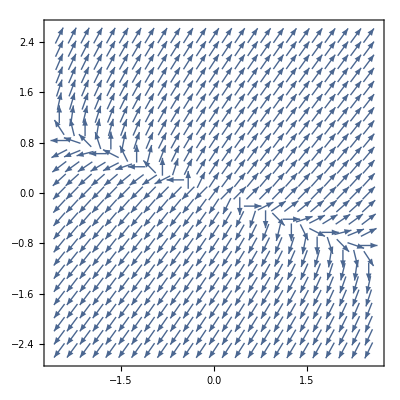

```mathematica
s12a=NDSolve[{x'[t]==x[t]+2y[t],y'[t]==1x[t]+3y[t],x[0]==-1,y[0]==0.4},{x,y},{t,10}];
plot12sa=ParametricPlot[Evaluate[{x[t], y[t]}/.s12a],{t,0,20},PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thick,Red}];
s12b=NDSolve[{x'[t]==x[t]+2y[t],y'[t]==1x[t]+3y[t],x[0]==1,y[0]==-0.4},{x,y},{t,10}];
plot12sb=ParametricPlot[Evaluate[{x[t], y[t]}/.s12b],{t,0,20},PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thick,Blue}];
s12c=NDSolve[{x'[t]==x[t]+2y[t],y'[t]==1x[t]+3y[t],x[0]==-0.1,y[0]==0.1},{x,y},{t,10}];
plot12sc=ParametricPlot[Evaluate[{x[t], y[t]}/.s12c],{t,0,20},PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thick,Orange}];
plot12=VectorPlot[{x+2y,x+3y},{x,-2.5,2.5},{y,-2.5,2.5},Axes->True,Frame->True,VectorScale->{Tiny,Automatic,None},VectorStyle->Arrowheads[.02],VectorPoints->Fine];
Show[plot12,plot12sa,plot12sb,plot12sc]
```